# FFT

## Demonstrate How FFT Works In Matrix Form

The discrete Fourier transform of a vector v is equivalent to 1/(√n)F v , where F is the matrix defined as follows:

```mathematica
(* DFT matrix *)
n=8;
F=Table[ⅇ^(ⅈ (2π i j)/n), {i, 0, n-1}, {j, 0, n-1}];
F//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | ⅇ^((ⅈ π)/4) | ⅈ | ⅇ^((3 ⅈ π)/4) | -1 | ⅇ^(-(3 ⅈ π)/4) | -ⅈ | ⅇ^(-(ⅈ π)/4)
1 | ⅈ | -1 | -ⅈ | 1 | ⅈ | -1 | -ⅈ
1 | ⅇ^((3 ⅈ π)/4) | -ⅈ | ⅇ^((ⅈ π)/4) | -1 | ⅇ^(-(ⅈ π)/4) | ⅈ | ⅇ^(-(3 ⅈ π)/4)
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | ⅇ^(-(3 ⅈ π)/4) | ⅈ | ⅇ^(-(ⅈ π)/4) | -1 | ⅇ^((ⅈ π)/4) | -ⅈ | ⅇ^((3 ⅈ π)/4)
1 | -ⅈ | -1 | ⅈ | 1 | -ⅈ | -1 | ⅈ
1 | ⅇ^(-(ⅈ π)/4) | -ⅈ | ⅇ^(-(3 ⅈ π)/4) | -1 | ⅇ^((3 ⅈ π)/4) | ⅈ | ⅇ^((ⅈ π)/4))

```mathematica
(* verify *)
v=Range[n];
((F.v)/(√n) -Fourier[v])//N//Chop
```

{0,0,0,0,0,0,0,0}

F can be decomposed into log n+1 sparse matrics. 
That’s why FFT can be done in O(n log n) computational time.

```mathematica
(* Decomposition for n=8 *)
B=({{1, 0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 0, ⅇ^(ⅈ (2π)/8), 0, 0}, {0, 0, 1, 0, 0, 0, ⅇ^(ⅈ (4π)/8), 0}, {0, 0, 0, 1, 0, 0, 0, ⅇ^(ⅈ (6π)/8)}, {1, 0, 0, 0, -1, 0, 0, 0}, {0, 1, 0, 0, 0, -ⅇ^(ⅈ (2π)/8), 0, 0}, {0, 0, 1, 0, 0, 0, -ⅇ^(ⅈ (4π)/8), 0}, {0, 0, 0, 1, 0, 0, 0, -ⅇ^(ⅈ (6π)/8)}}).({{1, 0, 1, 0, 0, 0, 0, 0}, {0, 1, 0, ⅈ, 0, 0, 0, 0}, {1, 0, -1, 0, 0, 0, 0, 0}, {0, 1, 0, -ⅈ, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 1, 0, ⅈ}, {0, 0, 0, 0, 1, 0, -1, 0}, {0, 0, 0, 0, 0, 1, 0, -ⅈ}}).({{1, 1, 0, 0, 0, 0, 0, 0}, {1, -1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0, 0, 0}, {0, 0, 1, -1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 1, -1}}).({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1}});
(* verify *)
B-F//N//Chop//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## The nth Root of Unity & DFT Matrix

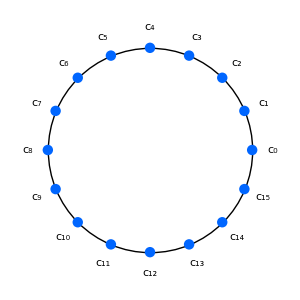

(c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0 | c_0
c_0 | c_1 | c_2 | c_3 | c_4 | c_5 | c_6 | c_7 | c_8 | c_9 | c_10 | c_11 | c_12 | c_13 | c_14 | c_15
c_0 | c_2 | c_4 | c_6 | c_8 | c_10 | c_12 | c_14 | c_0 | c_2 | c_4 | c_6 | c_8 | c_10 | c_12 | c_14
c_0 | c_3 | c_6 | c_9 | c_12 | c_15 | c_2 | c_5 | c_8 | c_11 | c_14 | c_1 | c_4 | c_7 | c_10 | c_13
c_0 | c_4 | c_8 | c_12 | c_0 | c_4 | c_8 | c_12 | c_0 | c_4 | c_8 | c_12 | c_0 | c_4 | c_8 | c_12
c_0 | c_5 | c_10 | c_15 | c_4 | c_9 | c_14 | c_3 | c_8 | c_13 | c_2 | c_7 | c_12 | c_1 | c_6 | c_11
c_0 | c_6 | c_12 | c_2 | c_8 | c_14 | c_4 | c_10 | c_0 | c_6 | c_12 | c_2 | c_8 | c_14 | c_4 | c_10
c_0 | c_7 | c_14 | c_5 | c_12 | c_3 | c_10 | c_1 | c_8 | c_15 | c_6 | c_13 | c_4 | c_11 | c_2 | c_9
c_0 | c_8 | c_0 | c_8 | c_0 | c_8 | c_0 | c_8 | c_0 | c_8 | c_0 | c_8 | c_0 | c_8 | c_0 | c_8
c_0 | c_9 | c_2 | c_11 | c_4 | c_13 | c_6 | c_15 | c_8 | c_1 | c_10 | c_3 | c_12 | c_5 | c_14 | c_7
c_0 | c_10 | c_4 | c_14 | c_8 | c_2 | c_12 | c_6 | c_0 | c_10 | c_4 | c_14 | c_8 | c_2 | c_12 | c_6
c_0 | c_11 | c_6 | c_1 | c_12 | c_7 | c_2 | c_13 | c_8 | c_3 | c_14 | c_9 | c_4 | c_15 | c_10 | c_5
c_0 | c_12 | c_8 | c_4 | c_0 | c_12 | c_8 | c_4 | c_0 | c_12 | c_8 | c_4 | c_0 | c_12 | c_8 | c_4
c_0 | c_13 | c_10 | c_7 | c_4 | c_1 | c_14 | c_11 | c_8 | c_5 | c_2 | c_15 | c_12 | c_9 | c_6 | c_3
c_0 | c_14 | c_12 | c_10 | c_8 | c_6 | c_4 | c_2 | c_0 | c_14 | c_12 | c_10 | c_8 | c_6 | c_4 | c_2
c_0 | c_15 | c_14 | c_13 | c_12 | c_11 | c_10 | c_9 | c_8 | c_7 | c_6 | c_5 | c_4 | c_3 | c_2 | c_1)

```mathematica
n=16;

(* the plot *)
Graphics[{PointSize[.025],Hue[.6],Point/@Table[{Cos[(2k π)/n],Sin[(2k π)/n]},{k,0,n-1}]},AspectRatio->Automatic,Axes->Automatic];
Graphics[Table[Text[Style[Subscript[c,k], Large],1.2{Cos[(2k π)/n],Sin[(2k π)/n]},{0,0}],{k,0,n-1}],AspectRatio->Automatic,Axes->Automatic];
Graphics[Circle[{0,0},1],AspectRatio->Automatic,Axes->Automatic];
Show[%,%%,%%%,ImageSize->300]

(* the matrix *)
Table[Subscript[c,Mod[i j,n]],{i,0,n-1},{j,0,n-1}]//MatrixForm
```

## FFT -- Cooley–Tukey Algorithm

There is built-in function Fourier[] which can evaluate the fast Fourier trnasform of a list. 
Here I write this to serve as a pseudo code so that i can impliment it in C.

```mathematica
FFT[aaa_]:=Block[{n, bbb, even, odd}, (* the length of the input must be a power of 2 *)
bbb=aaa;
n=Length[bbb];
If[n==1,
(* n==1 *)
Return[bbb], 

(* n≠1 *)
even=FFT[bbb[[2Range[n/2]-1]]];
odd=FFT[bbb[[2Range[n/2]]]] ⅇ^(2π ⅈ Range[0, n/2-1]/n);
Join[even+odd, even-odd]//Return;
];
];

IFFT[aaa_]:=Block[{n, bbb, even, odd}, (* the length of the input must be 2^k *)
bbb=aaa;
n=Length[bbb];
If[n==1,
(* n==1 *)
Return[bbb], 

(* n≠1 *)
even=IFFT[bbb[[2Range[n/2]-1]]];
odd=IFFT[bbb[[2Range[n/2]]]] ⅇ^(-2π ⅈ Range[0, n/2-1]/n);
Join[even+odd, even-odd]//Return;
];
];

(* verify *)
bbb={2, 3, 5, 7, 11, 13, 17, 19};
(FFT[bbb]//N)-Fourier[bbb] √8//Chop
(IFFT[bbb]//N)-InverseFourier[bbb] √8//Chop
```

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

## FRFT

The discrete Fourier transform evaluate ∑_(r=1)^n u_r e^(2π i(r-1)(s-1)/n). 
In some cases we need the fractional Fourier transform (FrFT) ∑_(r=1)^n u_r e^(2π i(r-1)(s-1)α). 
This can also be done in O(n log n) computations. 
The following algorithm is given by David H. Bailey & Paul N. Swarztrauber. 
Again, the built-in function Fourier[] which can do this. 
I just write this to serve as a pseudo code so that i can impliment it in C. 
Note that the inverse FrFT is unnecessary since α can be negative.

```mathematica
FrFT[aaa_, α_]:=Block[{y, z, n},(* output Table[ⅇ^(2 π ⅈ j k α), {k,0, n-1}, {j, 0, n-1}].aaa *)
n=Length[aaa]; 
y=PadRight[aaa ⅇ^(ⅈ π Range[0, n-1]^2 α), 2n];
z=Join[ⅇ^(-ⅈ π Range[0, n-1]^2 α), ⅇ^(-ⅈ π Range[n, 1, -1]^2 α)];
ⅇ^(ⅈ π Range[0, n-1]^2 α) (√(2n)Take[InverseFourier[Fourier[y] Fourier[z]], n])//Chop//Return;
];

(* with my own FFT[], the last line in the function should be:
ⅇ^(-ⅈ π Range[0, n-1]^2 α) (1/(2n)Take[IFFT[FFT[%%%] FFT[%%]], n])//N//Chop//Return;
*)

(* verify *)
bbb={2, 3, 5, 7, 11, 13, 17, 19};
n=Length[bbb];
a=√5;

(* my function *)
tt1=FrFT[bbb, a];

(* brute force *)
tt2=Table[ⅇ^(2π ⅈ j k a), {k,0, n-1}, {j, 0, n-1}].bbb//N;

(* built-in function *)
tt3=Fourier[bbb, FourierParameters->{1, a n}]//Chop;

{{tt1, tt2, tt3}}//TableForm
tt1-tt2//Chop
```

77.
-14.272-1.91872 ⅈ
-0.210611+8.33817 ⅈ
13.1626+3.66773 ⅈ
-11.5849-60.725 ⅈ
15.2433+13.7436 ⅈ
7.01947-8.43697 ⅈ
-6.85686-10.1127 ⅈ | 77.
-14.272-1.91872 ⅈ
-0.210611+8.33817 ⅈ
13.1626+3.66773 ⅈ
-11.5849-60.725 ⅈ
15.2433+13.7436 ⅈ
7.01947-8.43697 ⅈ
-6.85686-10.1127 ⅈ | 77.
-14.272-1.91872 ⅈ
-0.210611+8.33817 ⅈ
13.1626+3.66773 ⅈ
-11.5849-60.725 ⅈ
15.2433+13.7436 ⅈ
7.01947-8.43697 ⅈ
-6.85686-10.1127 ⅈ

{0,0,0,0,0,0,0,0}

## An Animation of Convolution

```mathematica
(* the two functions to be convolved *)
f[x_]:=1/(√(2π))ⅇ^(-x^2/2);
g[x_]:=1/(0.4 √(2π))ⅇ^(-(x/0.4)^2/2);
Export
Animate[
Plot[{g[x], f[a-x], g[x]f[a-x], 10Boole[x>a]}, {x, -5, 5}, 
PlotRange->{0, 1.2}, 
PlotStyle->{Hue[0], Hue[.6], Hue[.3], Hue[.3]}, 
Filling->{3->Bottom}, 
ImageSize->400]
,{a,-5,5},AnimationRunning->False]
```

Export

## The Plots of Probability Density Functions

In many option pricing models, only the characteristic function of the return of underlying asset are known analytically. 
In this case, to plot its probability density function, numerical methods can be used. 
By definition, the probability density function of a random variable is the inverse Fourier transform of its characteristic function, 
so the FFT algorithm can help to plot the density. 
Below the plots of density functions of five different models are given. 
The red line, the orange line, the green line, the blue line and the purple line are the density functions of Black-Scholes model, NIG model, CGMY model, Merton’s jump diffusion model, and double exponential model, respectively.

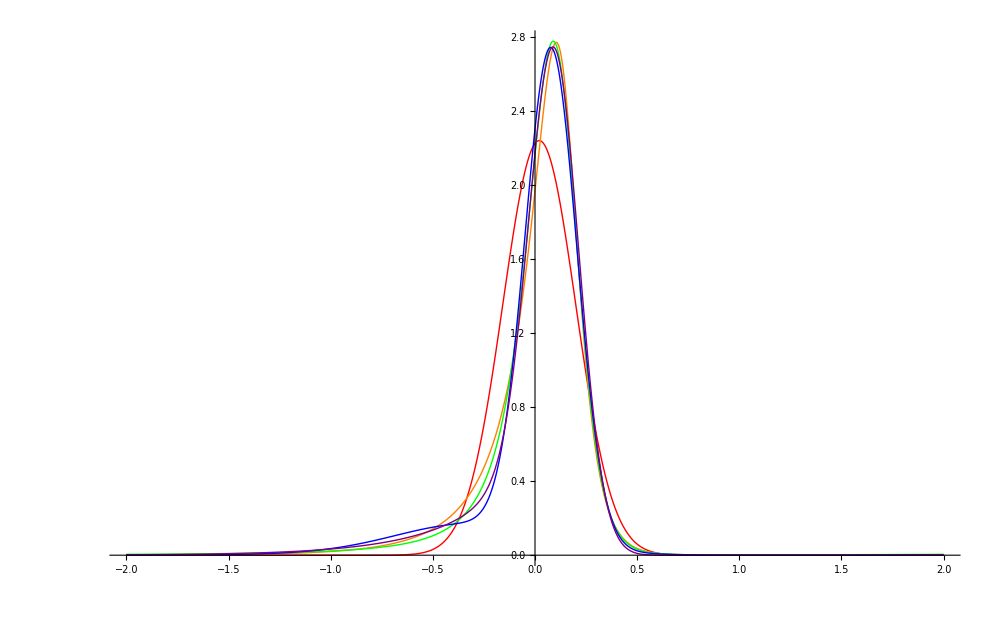

```mathematica
Clear[α, s, β, δ, c, G, M, Y, λ, r, dt, u, p, η];

m=1000;
a=-2;
b=2;
h=(b-a)/m;
xaxis=Range[a, b, h];

dt=1;
Adjustchf[chf_, r_, u_]:=chf[u] ⅇ^(ⅈ(r-Log[chf[-ⅈ]]/dt)dt u);(* in risk neutral world *)

parag={s->0.17801};
paranig={α->6.1882,β->-3.8941,δ->0.1622};
paracgmy={c->0.0244, G->0.0765, M->7.5515, Y->1.2945};
parajd={α->-0.390078, λ->0.174814, δ->0.338796, s->0.126349};
parade={p->0.2071, λ->0.330966, c->3.13868, η->9.65997, s->0.120381};

r=0.0367;

chfg[u_]:=ⅇ^(-(s^2 dt)/2 u^2)/.parag;
chfnig[u_]:=ⅇ^(-δ dt (√(α^2-(β+ⅈ u)^2)-√(α^2-β^2)))/.paranig;
chfcgmy[u_]:=ⅇ^(c Gamma[-Y]((M-ⅈ u)^Y-M^Y+(G+ⅈ u)^Y-G^Y)dt)/.paracgmy;
chfjd[u_]:=ⅇ^(-(s^2 dt)/2 u^2+λ dt (ⅇ^(ⅈ u α-1/2 u^2 δ^2)-1))/.parajd;
chfde[u_]:=ⅇ^(-(s^2 dt)/2 u^2+ λ dt(((1-p)c)/(c +ⅈ u)+(p η)/(η + ⅈ u)-1))/.parade;


ListLinePlot[{
{xaxis, 1/(2π)RotateRight[(RotateLeft[Adjustchf[chfg, r, (2 π)/((m+1)h^2)xaxis], m/2]//InverseFourier)√(m+1)(2 π)/((m+1)h), m/2]//Re}//Transpose, 
{xaxis, 1/(2π)RotateRight[(RotateLeft[Adjustchf[chfnig, r, (2 π)/((m+1)h^2)xaxis], m/2]//InverseFourier)√(m+1)(2 π)/((m+1)h), m/2]//Re}//Transpose, 
{xaxis, 1/(2π)RotateRight[(RotateLeft[Adjustchf[chfcgmy, r, (2 π)/((m+1)h^2)xaxis], m/2]//InverseFourier)√(m+1)(2 π)/((m+1)h), m/2]//Re}//Transpose, 
{xaxis, 1/(2π)RotateRight[(RotateLeft[Adjustchf[chfjd, r, (2 π)/((m+1)h^2)xaxis], m/2]//InverseFourier)√(m+1)(2 π)/((m+1)h), m/2]//Re}//Transpose, 
{xaxis, 1/(2π)RotateRight[(RotateLeft[Adjustchf[chfde, r, (2 π)/((m+1)h^2)xaxis], m/2]//InverseFourier)√(m+1)(2 π)/((m+1)h), m/2]//Re}//Transpose
}, PlotRange->All, ImageSize->1000, PlotStyle->{Red,Orange,Green, Blue, Purple}]
```

## Carr & Madan’s Option Pricing Algorithm

Here option values under variance-gamma model is evaluated with Carr & Madan’s option pricing algorithm. 
The output list gives the number of grid points, grid width, running time, and option value, respectively.

```mathematica
CM[s0_,K_,r_,T_,α_,η_,n_,chf_]:=
Block[{aa,Λ,bb,v,w,ku,call},
CPUTime=TimeUsed[];
Φ[u_]:=Log[chf[u,T]];
ϕ[u_]:=ⅇ^(ⅈ u Log[s0])ⅇ^(ⅈ u (r-Φ[-ⅈ]/T)T)chf[u,T];

ψ[u_]:=(ⅇ^(-r T)ϕ[(u-(α+1)ⅈ)])/(α^2+α-u^2+ⅈ(2α+1)u);
aa=n η;

Λ=(2 π)/(n η);
bb=(n Λ)/2-Log[K];

v=Delete[Range[0,aa,η],-1];

w=1/3 Table[3+(-1)^j-KroneckerDelta[j-1],{j,1,n}];

ku=Table[-bb+Λ(i-1),{i,1,n}];

call=ⅇ^(-α ku)/π InverseFourier[w Re[ⅇ^(ⅈ bb v)ψ[v]η],FourierParameters-> {-1,1}] ;

{aa,η,(TimeUsed[]-CPUTime),Re[call[[n/2+1]]]}//Return
];

Clear[chfvg,θ,ν,σ];
para={θ-> -0.1,ν->2 ,σ-> 0.25};
chfvg[u_,T_]:=(1-ⅈ θ ν u+1/2 σ^2 u^2 ν)^(-T/ν)/.para;
CM[100,77,0.02,0.25,1.5,.25,2^11,chfvg]
```

{512.,0.25,0.046,24.0244}